# Quadratic Penalty Methods min f[x] g_e[x]=0 and/or g_i[x]≥0

## Visualization

### Equality Constraints min f[x] with g_(1:n)[x]=0

The plan is to incorporate the constraints into a modified objective function  
	f[x]+μ/2∑_(i=1)^n (g_i[x])^2 
and use the unconstrained minimization techniques we have developed.  First we need to get an idea of how well this could work. The big picture is to solve a sequence of problems with increasing values of the penalization parameter μ_k.  Hopefully when μ is big the solution almost satisfies the constraints g[x]==0 and almost minimizes the original objective function f.

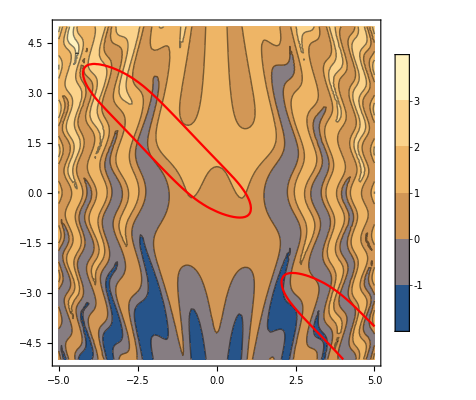

```mathematica
f[{x1_,x2_}]:= Sin[x1^2+ Cos[x1 x2]]+0.05 (x1^2-0.3 x1 x2 + 4 x2)
g[{x1_,x2_}]:= Sin[x2 + Cos[x1-ArcTan[x1 + x2]]]-(x1+x2)^2
Q[x_,μ_]:=f[x]+μ/2 g[x]^2
Show[
ContourPlot[f[{x1,x2}],{x1,-5,5},{x2,-5,5},PlotLegends->Automatic],
ContourPlot[g[{x1,x2}]==0,{x1,-5,5},{x2,-5,5},ContourStyle->Red]
]
```

The main problem is sensitivity w.r.t μ

```mathematica
Manipulate[
Show[
ContourPlot[Q[{x1,x2},μ],{x1,-5,5},{x2,-5,5},PlotRange->{-2,4}],
ContourPlot[g[{x1,x2}]==0,{x1,-5,5},{x2,-5,5},ContourStyle->Red]
],
{μ,{0,0.01,0.1,1,10,100}}]
```

The second problem is that the gradient and Hessian of the modified objective become dominated by the penalty terms.  
	∇Q | = | ∇f+μ ∑_(i=1)^n g_i ∇g_i                                
∇^2 Q | = | ∇^2 f+μ ∑_(i=1)^n (g_i ∇^2 g_i+∇g_i⊗∇g_i)
As a direct result the linear algebra required to solve the constrained problem for Q becomes increasingly ill conditioned as you increase μ.  When μ is big there is very little of the original objective function left in Q.

To be any use we must be near the constraint set. Near the constraint set g_i is small! As a rough estimate, the penalty term 
	μ ∑_(i=1)^n g_i ∇g_i 
in the gradient is of size μ×small near the constraint set.  Also as a rough estimate the penalty term 
	 μ∑_(i=1)^n (g_i ∇^2 g_i+∇g_i⊗∇g_i)
in the Hessian is dominated as μ gets big by the rank n term
	 μ∑_(i=1)^n ∇g_i⊗∇g_i
near the constraint set.  There is nothing small in this term and as μ increases ∇^2 Q≈ μ∑_(i=1)^n ∇g_i⊗∇g_i. In words, as μ gets big the hessian becomes increasingly ill conditioned.

### Inequality Constraints min f[x] with g_(1:n)[x]≥0

The plan is to incorporate the constraints into a modified objective function  
	f[x]+μ/2∑_(i=1)^n If[g_i[x]≤0,g_i[x]^2,0] 
and use the unconstrained minimization techniques we have developed.  First we need to get an idea of how well this could work. The big picture is to solve a sequence of problems with increasing values of the penalization parameter μ_k.  Hopefully when μ is big the solution almost satisfies the constraints g[x]==0 and almost minimizes the original objective function f.

```mathematica
f[{x1_,x2_}]:= Sin[x1^2+ Cos[x1 x2]]+0.05 (x1^2-0.3 x1 x2 + 4 x2)
g[{x1_,x2_}]:= Sin[x2 + Cos[x1-ArcTan[x1 + x2]]]-(x1+x2)^2
Q[x_,μ_]:=f[x]+μ/2 If[g[x]≤0,g[x]^2,0]
Manipulate[
Show[
ContourPlot[Q[{x1,x2},μ],{x1,-5,5},{x2,-5,5},PlotRange->{-2,4}],
ContourPlot[g[{x1,x2}]==0,{x1,-5,5},{x2,-5,5},ContourStyle->Red]
],
{μ,{0,0.01,0.1,1,10,100}}]
```

The main problem is the same sensitivity w.r.t μ.  Note if the constrained min is on the edge of the feasible region the penalized min is going to be just outside the feasible region where the penalty term is active.  The Hessian is messed up by the same low rank term 
	 μ∑_(i=1)^n ∇g_i⊗∇g_i	
as in the equality constrained problem.

### Inequality Constraints (with a log barrier) min f[x] with g_(1:n)[x]≥0

The plan is to incorporate the constraints into a modified objective function  
	f[x]-ϵ∑_(i=1)^n Log[g_i[x]] 
and use the unconstrained minimization techniques we have developed.  First we need to get an idea of how well this could work. The big picture is to solve a sequence of problems with increasing values of the penalization parameter μ_k.  Hopefully when μ is big the solution almost satisfies the constraints g[x]==0 and almost minimizes the original objective function f.

```mathematica
f[{x1_,x2_}]:= Sin[x1^2+ Cos[x1 x2]]+0.05 (x1^2-0.3 x1 x2 + 4 x2)
g[{x1_,x2_}]:= Sin[x2 + Cos[x1-ArcTan[x1 + x2]]]-(x1+x2)^2
QLog[x_,ϵ_]:=f[x]+ϵ Log[g[x]]
Manipulate[
Show[
ContourPlot[QLog[{x1,x2},ϵ],{x1,-5,5},{x2,-5,5},PlotRange->{-2,4}],
ContourPlot[g[{x1,x2}]==0,{x1,-5,5},{x2,-5,5},ContourStyle->Red]
],
{ϵ,{1,0.1,0.01,0.001, 0.0001}}]
```

The main problem is the same sensitivity w.r.t μ.  Note if the constrained min is on the edge of the feasible region the penalized min is going to be just outside the feasible region where the penalty term is active.  The Hessian is messed up by the same low rank term 
	 μ∑_(i=1)^n ∇g_i⊗∇g_i	
as in the equality constrained problem.

## Algorithmic Framework “l-2” 17.1 p501/523

## Algorithmic Framework “l-1” 17.2 p511/533

## Augmented Lagrangian: Equality Constraints 17.3 p514/536

In the quadratic penalty setup with equality constraints we have  
	c_i(x_k)≈-λ_i/μ_k  as k→∞
To avoid clutter we have been writing this as a vector
	c(x_k)≈-λ/μ_k
The Augmented Lagrangian idea is to include this term as an explicit estimate for the multipliers
	ℒ_A(x,λ;μ):=f(x)-λ.c(x)+(μ/2)c(x).c(x)
in the quadratic penalty function. This looks like the standard Lagrangian with the quadratic penalty added.   It looks as though there should be a μ in the middle term somewhere.  However computing the gradient (to get the stationary condition for the Augmented Lagrangian at a fixed set of estimated multipliers λ_k and a fixed penalization parameter μ_k) we have 
	0 | =∇_x ℒ_A(x,λ_k;μ_k) | = | ∇f(x) | -(λ_k-μ_k c(x))∇c(x)
while the equivalent condition for the constrained problem is
	0 | =∇_x ℒ(x,λ) | = | ∇f(x) | -λ c(x)∇c(x)
comparing these we see that near the constrained min (in a practical sense means μ_k is big and everything is working)
	λ | ≈ | λ_k-μ_k c(x_k)
Two things coming from this.

Since
	c(x_k) | ≈ | -1/μ_k(λ-λ_k)
the constraint violation is much smaller if λ_k is approximately correct.

We have a good idea of how to update the approximation λ_k for the next step.
	λ_(k+1) | = | λ_k-μ_k c(x_k).

This is all wrapped up together in Framework 17.3.  Theorem 17.5 says that once μ is big enough you lock onto a genuine local min.